```mathematica
data365= {{-1.1,0},{4.1, 84*10^(-10)},{9.1, 168*10^(-10)},{14.1, 236*10^(-10)},{19.1, 281*10^(-10)},{24.1, 331*10^(-10)}, {30.71, 378*10^(-10)}}
```

{{-1.1,0},{4.1,21/2500000000},{9.1,21/1250000000},{14.1,59/2500000000},{19.1,281/10000000000},{24.1,331/10000000000},{30.71,189/5000000000}}

```mathematica
data436 = {{-0.76,0},{2.78,23*10^(-10)},{4.74, 36*10^(-10)},{6.78, 43*10^(-10)},{8.77, 50*10^(-10)},{10.78, 58*10^(-10)},{12.76, 65*10^(-10)}}
```

{{-0.76,0},{2.78,23/10000000000},{4.74,9/2500000000},{6.78,43/10000000000},{8.77,1/200000000},{10.78,29/5000000000},{12.76,13/2000000000}}

```mathematica
data577 = {{-0.02,0},{5, 212*10^(-11)},{10.02, 284*10^(-11)},{15.03, 350*10^(-11)},{20.04, 398*10^(-11)},{25.02, 436*10^(-11)},{30.72, 436*10^(-11)}}
```

{{-0.02,0},{5,53/25000000000},{10.02,71/25000000000},{15.03,7/2000000000},{20.04,199/50000000000},{25.02,109/25000000000},{30.72,109/25000000000}}

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(19 Frame)/500000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

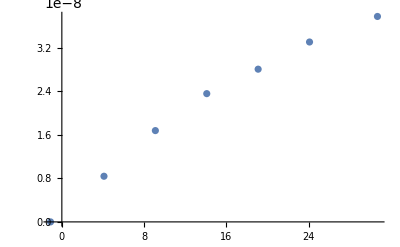

```mathematica
ListPlot[data365, PlotRange->{{31},{380*10^(-10)}} Frame -> True,
 FrameLabel ->{"Voltage", "Current"}]
```

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(19 Frame)/500000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

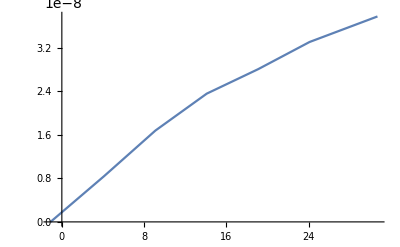

```mathematica
ListPlot[data365, PlotRange->{{31},{380*10^(-10)}} Frame -> True,
 FrameLabel ->{"Voltage", "Current"}, Joined -> True]
```

```mathematica
Fit[data365, {1,x}, x]
```

4.07336×10^-9+1.19155×10^-9 x

ListPlot::prng: Value of option PlotRange -> {{13 Frame},{(7 Frame)/1000000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

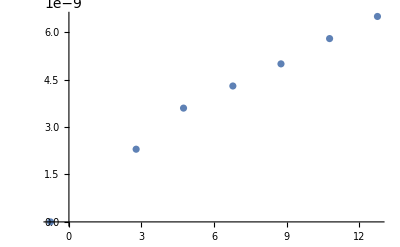

```mathematica
ListPlot[data436, PlotRange->{{13},{70*10^(-10)}} Frame -> True,
 FrameLabel ->{"Voltage", "Current"}]
```

ListPlot::prng: Value of option PlotRange -> {{13 Frame},{(7 Frame)/1000000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

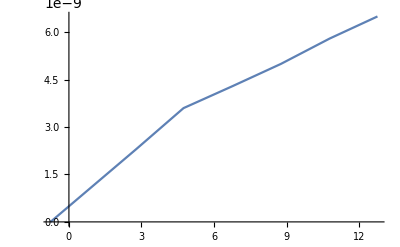

```mathematica
ListPlot[data436, PlotRange->{{13},{70*10^(-10)}} Frame -> True,
 FrameLabel ->{"Voltage", "Current"}, Joined -> True]
```

```mathematica
Fit[data436, {1,x}, x]
```

8.7035×10^-10+4.66904×10^-10 x

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(11 Frame)/2500000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

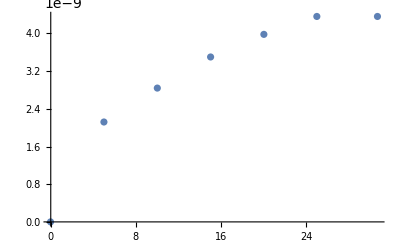

```mathematica
ListPlot[data577, PlotRange->{{31},{440*10^(-11)}} Frame -> True,
 FrameLabel ->{"Voltage", "Current"}]
```

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(11 Frame)/2500000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

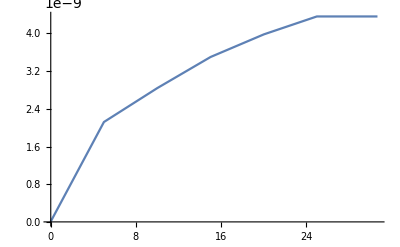

```mathematica
ListPlot[data577, PlotRange->{{31},{440*10^(-11)}} Frame -> True,
 FrameLabel ->{"Voltage", "Current"}, Joined -> True]
```

```mathematica
Fit[data577, {1,x}, x]
```

1.04571×10^-9+1.30801×10^-10 x